Definition of the Potential

```mathematica
r[x_]:= x+ r0
r0 = 1/(4 OverTilde[a]);
Veff[x_] := 1/(8r[x]^2) -OverTilde[a]/r[x] + 2OverTilde[a]^2
```

First Coefficients

```mathematica
phiminusone[x_]:= Assuming[x>=0&&OverTilde[a]>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
Eminustwo = -2OverTilde[a]^2;
Es = {Eminustwo};
phis = {phiminusone[x]};
Eminusone = -1/2(D[phis[[1]],x] /. x-> 0)-1/(2 r[0]^2);
AppendTo[Es,Eminusone];
phizero[s_] :=Simplify[( Es[[2]] + 1/(2r[s]^2) +1/2(D[phis[[1]],x] /.x->s))/(-phiminusone[s])]
AppendTo[phis,phizero[x]];

Ezero = 3/(8 r[0]^2)-1/2(D[phis[[2]],x]/. x->0)-1/2( phis[[2]]^2 /. x->0) +(9b)OverTilde[a];
phione[s_] := Simplify[(-3/(8 r[s]^2)+1/2(D[phis[[2]],x]/. x->s)+1/2( phis[[2]]^2 /. x->s) -(9b)OverTilde[a]+ Ezero)/(-phiminusone[s])]
```

Recursion Relation

```mathematica
Energy[n_]:= Energy[n] = Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,EvenQ[n],Simplify[-1/2(D[phi[n],x]/.x->0)-1/2Sum[(phi[m]/.x->0)(phi[n-m]/. x->0),{m,0,n}]+(-1)^(n/2)(9b)^(n/2+1)/Factorial[n/2+1]OverTilde[a]r[0]^(n/2)],True,Simplify[-1/2(D[phi[n],x]/.x->0)-1/2Sum[(phi[m]/.x->0)(phi[n-m]/. x->0),{m,0,n}]]]
phi[n_]:= phi[n] = Which[n==-1,phiminusone[x],n==0,phizero[x],n==1,phione[s],OddQ[n],Simplify[(Energy[n-1]+ 1/2 D[phi[n-1],x]+1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]+(-1)^((n+1)/2)(9b)^((n+1)/2)/Factorial[(n+1)/2]OverTilde[a]r[x]^((n-1)/2))/(-phiminusone[x])],True,Simplify[(Energy[n-1]+ 1/2 D[phi[n-1],x]+1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}])/(-phiminusone[x])]]
```

```mathematica
Clear[Energy,phi]
```

Redefinitions

```mathematica
OverTilde[a] = 1/k^2;
```

```mathematica
maxkOrder = 140;
ProgressIndicator[Dynamic[n],{0,maxkOrder}]
times = Table[Timing[Energy[n]][[1]],{n,-2,maxkOrder}];
```

```mathematica
perturbationorder = 35;
EnergySeries = Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder}],k],b]],b]+O[b]^(perturbationorder+1)];
Coefficients = {-2/(k-1)^2};
Do[AppendTo[Coefficients,Collect[Coefficient[EnergySeries, b,n],k] ],{n,1,perturbationorder}]
Table[Length[Coefficients[[(n+1)]] /. Sum ->List]==2(n-1),{n,2,perturbationorder}]
```

35

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

3

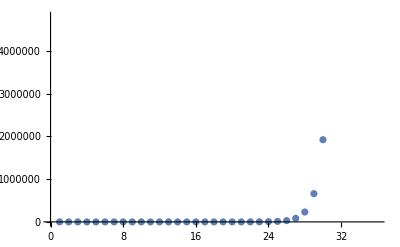

```mathematica
k=3
PertrubativeFactors = {1};
Do[AppendTo[PertrubativeFactors,b^n],{n,1,perturbationorder}]
RelativeError = Coefficients*PertrubativeFactors;
ListPlot[Abs[RelativeError /. b->0.5]]
```

```mathematica
ListPlot[Abs[Coefficients]]
```

-Graphics-

```mathematica
N[Normal[(EnergySeries )]/. b -> 0.1]
```

-0.407058

```mathematica
PadeApproximation = PadeApproximant[EnergySeries,{b,0,Floor[perturbationorder/2]}] ;
NumberForm[PadeApproximation /. b-> 0.5,20]
```

-0.1481170218899362

```mathematica
PartialSums = Table[Total[Take[Coefficients,order+1]*Table[b^n,{n,0,order}]],{order,0,perturbationorder}];
PadeNN = Table[PadeApproximant[PartialSums[[n]],{b,0,Floor[n/2]}] ,{n,3,perturbationorder}];
PadeNNplusone = Table[PadeApproximant[PartialSums[[n]],{b,0,{Floor[n/2],Floor[n/2]+1}}] ,{n,3,perturbationorder}];
```

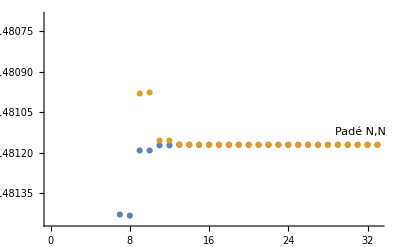

```mathematica
PadeAproximationsnn = Table[(PadeNN[[n-2]] /. b->0.5),{n,3,perturbationorder}];
PadeAproximationsnplusone = Table[(PadeNNplusone[[n-2]] /. b->0.5),{n,3,perturbationorder}];
ListPlot[{Labeled[PadeAproximationsnn,"Padé N,N",Right],Labeled[PadeAproximationsnplusone,"Padé N,N+1",Left]}]
```

0.25

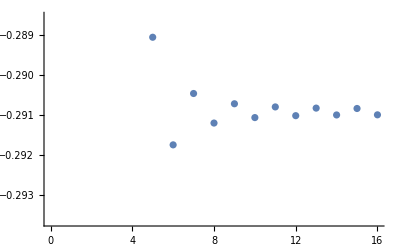

-0.290999

-0.29092

```mathematica
value = 0.25
bestindex =Position[Abs[RelativeError /. b->value],Min[Abs[RelativeError /. b->value]]][[1,1]];
ListPlot[Table[PartialSums[[s]],{s,0,bestindex}] /. b-> value]
BestasymAprox = PartialSums[[bestindex]] /. b->value
BestEstimatePade= PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->value
```

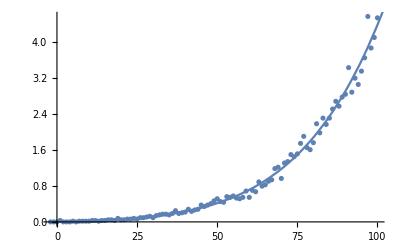

```mathematica
ns = Table[n,{n,-2,100}];
data = Table[{ns[[n]],times[[n]]},{n,1,103}];
model = Fit[data,Table[x^(n),{n,0,5}],x];
Show[ListPlot[data],Plot[model,{x,-2,1000}]]
```